```mathematica
data=Import["/Users/linaruiz/Documents/projectEpidemicCurve/data/wavesSizes.csv"];
data[[;;10]]//Grid
```

Country | cunsum | max | sum | max/Max
Belgium | 0 | 0.0202451 | 0.529787 | 0.0308678
Belgium | 1 | 0.19232 | 5.14826 | 0.293231
Belgium | 2 | 0.054214 | 3.63995 | 0.0826604
Belgium | 3 | 0.221039 | 7.7731 | 0.33702
Belgium | 4 | 0.655864 | 14.0276 | 1.
Belgium | 5 | 0.156276 | 4.73141 | 0.238275
Belgium | 6 | 0.106962 | 2.92253 | 0.163085
Belgium | 7 | 0.031338 | 0.357226 | 0.0477813
Bosnia and Herzegovina | 0 | 0.00277241 | 0.0598781 | 0.0271347

```mathematica
data[[2]]
```

{Belgium,0,0.0202451,0.529787}

```mathematica
data2=Table[MapAt[{i,#}&,GroupBy[data[[2;;]],First][[i]],{All,-3;;-1}],{i,1,15}];
data2[[;;2]]
```

{{{Belgium,0,{1,0.0202451},{1,0.529787},{1,0.0308678}},{Belgium,1,{1,0.19232},{1,5.14826},{1,0.293231}},{Belgium,2,{1,0.054214},{1,3.63995},{1,0.0826604}},{Belgium,3,{1,0.221039},{1,7.7731},{1,0.33702}},{Belgium,4,{1,0.655864},{1,14.0276},{1,1.}},{Belgium,5,{1,0.156276},{1,4.73141},{1,0.238275}},{Belgium,6,{1,0.106962},{1,2.92253},{1,0.163085}},{Belgium,7,{1,0.031338},{1,0.357226},{1,0.0477813}}},{{Bosnia and Herzegovina,0,{2,0.00277241},{2,0.0598781},{2,0.0271347}},{Bosnia and Herzegovina,1,{2,0.0588535},{2,3.56463},{2,0.576022}},{Bosnia and Herzegovina,2,{2,0.0658526},{2,2.59494},{2,0.644524}},{Bosnia and Herzegovina,3,{2,0.0383681},{2,1.97246},{2,0.375524}},{Bosnia and Herzegovina,4,{2,0.102172},{2,3.30758},{2,1.}},{Bosnia and Herzegovina,5,{2,0.020728},{2,0.632417},{2,0.202873}}}}

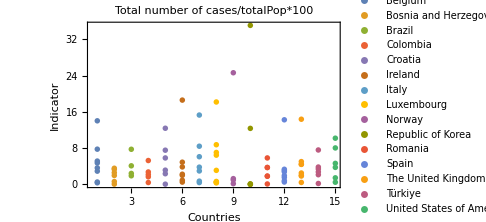
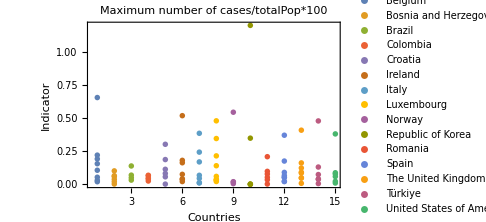
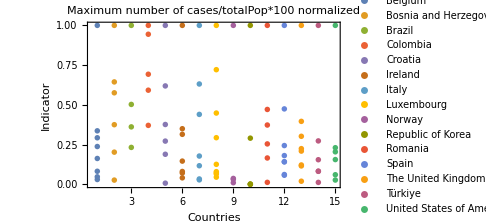

```mathematica
listPlot=ListPlot[#[[1]],PlotLabel->#[[2]],PlotRange->All,ImageSize->Medium,Frame->True,FrameLabel->{"Countries","Indicator"},PlotLegends->data2[[All,1,1]]]&/@{{data2[[All,All,-2]],"Total number of cases/totalPop*100"},
{data2[[All,All,-3]],"Maximum number of cases/totalPop*100"},
{data2[[All,All,-1]],"Maximum number of cases/totalPop*100 normalized"}}
```

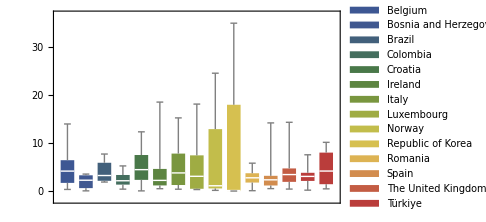
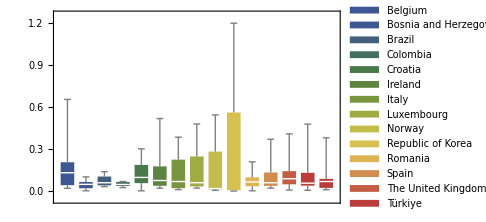
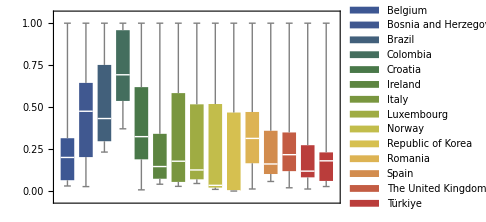

```mathematica
data3=GroupBy[data,First];
boxPlot=BoxWhiskerChart[#[[1]],ChartLabels->#[[2]],ChartLegends->Automatic, ChartStyle->"DarkRainbow",ImageSize->Medium]&/@{
{data3[[2;;,All,-2]],"Total number of cases/totalPop*100"},
{data3[[2;;,All,-3]],"Maximum number of cases/totalPop*100"},
{data3[[2;;,All,-1]],"Maximum number of cases/totalPop*100 normalized"}}
```

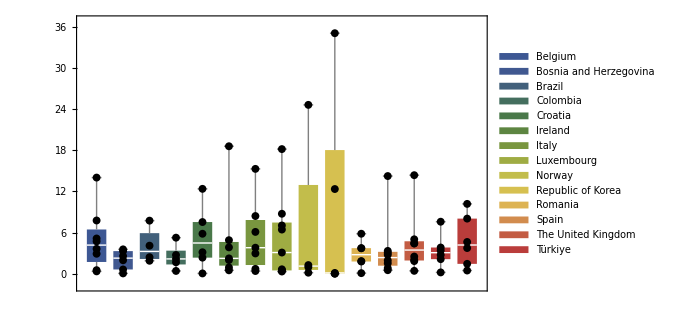
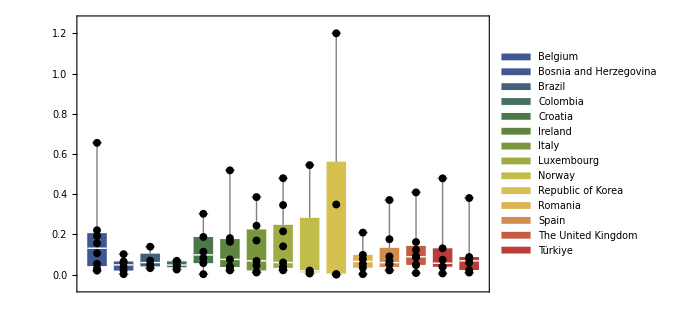
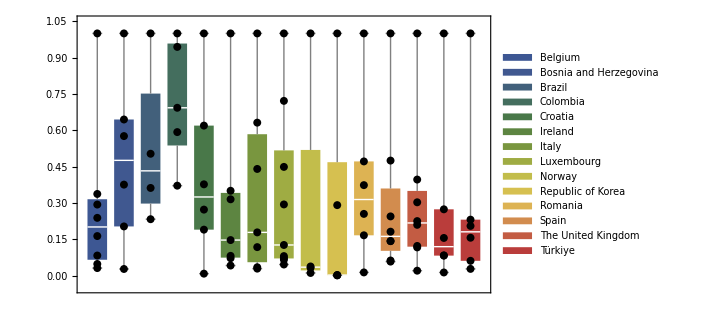

```mathematica
listPlot2=ListPlot[#[[1]],PlotLabel->#[[2]],PlotRange->All,ImageSize->Medium,Frame->True,FrameLabel->{"Countries","Indicator"},PlotStyle->Black]&/@{{data2[[All,All,-2]],"Total number of cases/totalPop*100"},
{data2[[All,All,-3]],"Maximum number of cases/totalPop*100"},
{data2[[All,All,-1]],"Maximum number of cases/totalPop*100 normalized"}};

Show[boxPlot[[#]],listPlot2[[#]]]&/@{1,2,3}
```

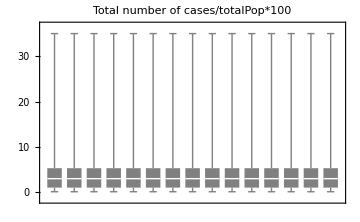
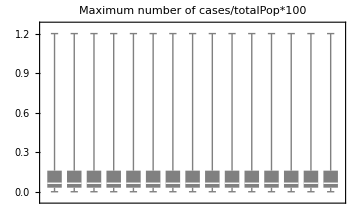
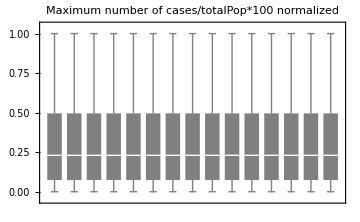

```mathematica
allBoxPlot=BoxWhiskerChart[Table[Flatten@GatherBy[data[[2;;]],First][[All,All,#[[1]]]],Length[data2[[All,1,1]]]],PlotLabel->#[[2]],ImageSize->Medium,ChartStyle->Gray]&/@{
{-2,"Total number of cases/totalPop*100"},
{-3,"Maximum number of cases/totalPop*100"},
{-1,"Maximum number of cases/totalPop*100 normalized"}}
```

```mathematica
Show[allBoxPlot[[#]],listPlot[[#]]]&/@{1,2,3}
```